```mathematica
data ={{10.8,11.1},{20.1,20.5},{40.9,30.4},{60.2,55.6},{90.3,83.2},{120,127},{151,140},{181,148},{210,157},{240,165},{270,163},{300,167},{330,174}}
```

```mathematica
fit = NonlinearModelFit[data,1/2*d*200*(1/d*Exp[-d*t]-1/c*Exp[-c*t]+1/c-1/d),{c,d},t]
Lösung des Mass-Action-DGL Systems
```

NonlinearModelFit::fitd: First argument data in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[data,100 d (1/c-1/d-ⅇ^(-c t)/c+ⅇ^(-d t)/d),{c,d},t]

-Action+des Lösung Mass-DGL Systems

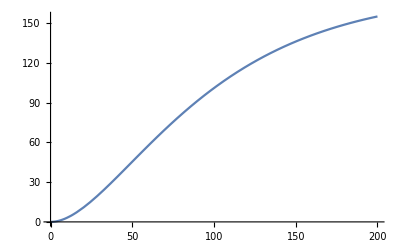

```mathematica
Plot[fit[t],{t,0,200}]
```

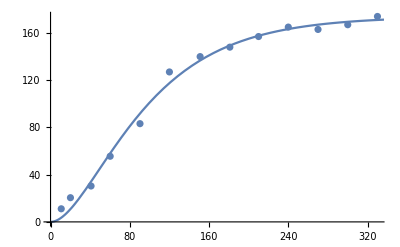

```mathematica
Show[ListPlot[data],Plot[fit[t],{t,0,350}]]
```

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c | 0.0147564 | 0.000728587 | 20.2534 | 4.66891×10^-10
d | 0.0275861 | 0.00116363 | 23.7069 | 8.5641×10^-11

```mathematica
data2 = {{10.8,11.1},{20.1,20.5},{40.9,30.4},{60.2,55.6},{90.3,83.2},{120,127}}
```

{{10.8,11.1},{20.1,20.5},{40.9,30.4},{60.2,55.6},{90.3,83.2},{120,127}}

```mathematica
LinearModelFit[data2, x, x]
```

FittedModel[-4.55203+1.03743 x]

```mathematica
data3 = {{10.8,1.0374297143341766},{20.1,1.0374297143341766},{40.9,1.0374297143341766},{60.2,1.0374297143341766},{90.3,1.0374297143341766},{120,1.0374297143341766}}
```

{{10.8,1.03743},{20.1,1.03743},{40.9,1.03743},{60.2,1.03743},{90.3,1.03743},{120,1.03743}}

```mathematica
fit2 = NonlinearModelFit[data3,0.5*d(1/(d*t-1/200)+200*Exp[-c*t])^2,{c,d},t]
```

FittedModel[0.0021027 (200 ⅇ^(-«18» t)+1/(-1/200«1»«21»«1»«1»))^2]

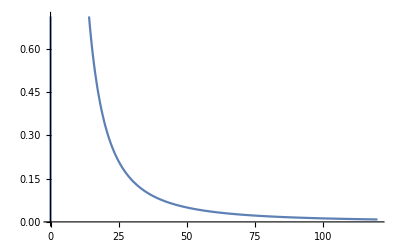

```mathematica
Plot[fit2[t],{t,0,120}]
```

```mathematica
data4 = Import["/Users/friedrich/Desktop/hemoz change.csv","Table"]
```

{{24.75,1.01075},{51.3,0.475962},{69.85,1.3057},{105.35,0.916944},{134.85,1.47475},{166.5,0.419355},{196,0.266667},{224.5,0.310345},{255,0.266667},{285,-0.0666667},{315,0.133333},{345,0.233333}}

```mathematica
fit3 = NonlinearModelFit[data4,0.5*d(1/(d*t-1/200)+200*Exp[-c*t])^2,{c,d},t]
```

FittedModel[0.000523639 (200 ⅇ^(-«19» t)+1/(-1/200«1»«22»«1»«1»))^2]

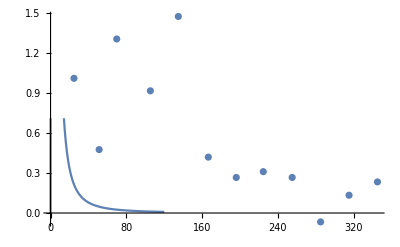

```mathematica
Show[ListPlot[data4],Plot[fit2[t],{t,0,120}]]
```

```mathematica
data5 ={{10.8,11.1},{20.1,20.5},{40.9,30.4},{60.2,55.6},{90.3,83.2},{120,127},{151,140},{181,148},{210,157},{240,165},{270,163},{300,167},{330,174}}
```

{{10.8,11.1},{20.1,20.5},{40.9,30.4},{60.2,55.6},{90.3,83.2},{120,127},{151,140},{181,148},{210,157},{240,165},{270,163},{300,167},{330,174}}

```mathematica
fit5 = NonlinearModelFit[data5,1/2*d*200*(1/d*Exp[-d*t]-1/c*Exp[-c*t]+1/c-1/d),{c,d},t]
```

FittedModel[3.48281 (50.6616+28.7124 ⅇ^(-«19» t)-79.374 ⅇ^(-0.0125986 t))]

```mathematica
fit5["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c | 0.0125986 | 0.000691822 | 18.2107 | 1.45709×10^-9
d | 0.0348281 | 0.00152098 | 22.8985 | 1.24561×10^-10

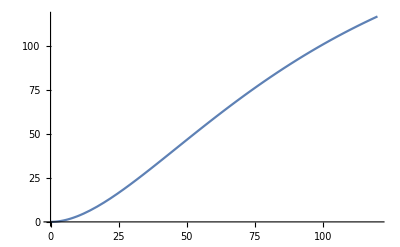

```mathematica
Plot[fit5[t], {t,0,120}]
```

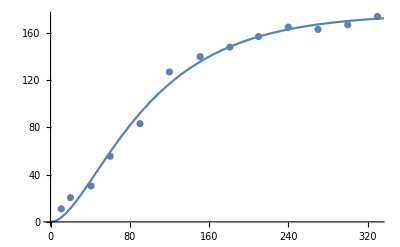

```mathematica
Show[ListPlot[data5],Plot[fit5[t],{t,0,500}]]
```

```mathematica
data6 = Import["/Users/friedrich/Desktop/hz(s0).csv","Table"]
```

```mathematica
{{0,0},{41.2,14.6},{101,51.6},{200,104},{240,120},{299,151},{501,216},{600,236},{400,200}}
data7 = {{0,0},{41.2,14.6},{101,51.6},{200,104},{240,120},{299,151},{400,200}}
```

{{0,0},{41.2,14.6},{101,51.6},{200,104},{240,120},{299,151},{501,216},{600,236},{400,200}}

{{0,0},{41.2,14.6},{101,51.6},{200,104},{240,120},{299,151},{400,200}}

```mathematica
fit9 = NonlinearModelFit[data7,1/2*d*s*(1/d*Exp[-d*500]-1/c*Exp[-c*500]+1/c-1/d),{c,d},s]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[0.503099 s]

```mathematica
fit9["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c | 11.1743 | 0.048038 | 232.614 | 2.78634×10^-11
d | 22.4179 | 0.0239448 | 936.235 | 2.63861×10^-14

```mathematica
fit9["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c | 0.438667 | 0.000440471 | 995.904 | 2.56392×10^-26
d | 0.44002 | 0.000439117 | 1002.06 | 2.4108×10^-26

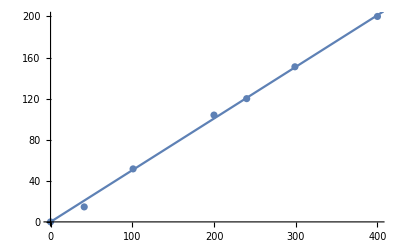

```mathematica
Show[ListPlot[data7],Plot[fit9[s],{s,0,600}]]
```

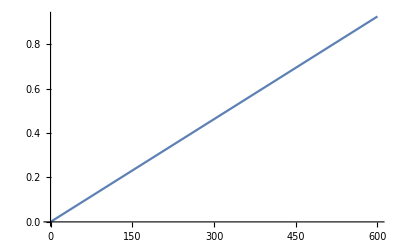

```mathematica
Plot[fit9[s],{s,0,600}]
```